# Import J from cs_dump2

Verifying/tuning the conjugate gradient (Krylov subspace) solver.

```mathematica
$base=NotebookDirectory[]~FileNameJoin~"temp";
"s3d132 partition 0 of 27";
$j=Import[$base~FileNameJoin~"J2.txt","Table"];
$b=1.Flatten@Rest@Import[$base~FileNameJoin~"minusFx.txt","Table"];

$js=$j//First;

$jd=($j//Rest(*extra rest: skip NNZ, can be inferred*)//Rest);
$jd=Function[{i,j,x},{i,j}+1->1.x]@@@$jd;

$jm=SparseArray[$jd,$js,0.];
Dimensions@$jm
Dimensions@$b

$sol=LeastSquares[$jm,$b,Method->"Krylov"]
```

{5632,1024}

{5632}

{-0.0798112,-0.0245212,-0.196619,-0.000166972,-0.183393,0.00536891,-0.164539,0.0120736,-0.159137,0.0104399,0.,0.020066,0.,0.0282988,0.00934962,0.0199154,-0.0798112,0.0393054,-0.0395972,-0.0958668,-0.0257601,-0.110798,-0.0247981,-0.0596932,-0.0259589,-0.0855294,-0.952346,0.0282647,-0.803856,0.0443634,-0.017732,-0.00742627,-0.0262806,-0.0194737,-0.0215385,-0.0880088,-0.0170245,-0.0973191,-0.0155847,-0.0686749,-0.01609,-0.032531,-0.018256,-0.0292726,-0.0165553,-0.0239259,-0.00961607,-0.0493267,-0.00818111,-0.0353451,-0.00921369,-0.0734716,-0.0094051,-0.0560892,-0.00853818,-0.0557275,-0.00838659,-0.0242666,-0.00777907,-0.0193857,-0.00664462,-0.00573996,-0.0042105,-0.0183074,-0.00506411,-0.0392157,-0.00732426,-0.0745406,-0.00967222,-0.102329,-0.00687515,-0.098832,-0.0061551,-0.0420915,-0.00441005,-0.0246431,-0.00355158,-0.00543531,-0.00245038,-0.0193809,-0.00401863,0.0786313,-0.00923411,0.0256576,-0.856372,0.0281806,-0.0111693,-0.188952,-0.00548561,-0.0726365,-0.00285417,-0.0534495,-0.00220466,-0.0311093,-0.00156052,-0.0151369,-0.00204206,0.0143002,-0.00562701,0.00746693,0.,0.00244569,-0.0111693,0.0431463,-0.00548561,0.0686777,0.183235,0.0622324,-0.00160307,-0.0651344,-0.00130469,-0.025592,-0.00204206,0.00107518,0.,-0.00683663,0.,0.011943,0.,0.00836196,0.,0.0255994,0.,-0.00478925,-0.310654,0.100214,-0.00234957,-0.0362759,-0.840218,-0.0349317,-0.242869,-0.0182671,-0.735058,0.00723804,-1.07287,-0.00354164,-0.130535,0.0016395,-0.299215,0.0137958,0.,0.0215465,0.,0.0235613,-0.047535,-0.034781,-0.042149,-0.0770834,-0.185145,-0.0386521,-0.165759,-0.0494434,-0.0267655,-0.0801611,-0.0220423,-0.059473,-0.977178,0.0468425,-0.277555,0.0199117,-0.0187894,-0.0387105,-0.0194433,-0.0911963,-0.0169068,-0.102351,-0.0162183,-0.0835372,-0.0168967,-0.0617054,-0.0162997,-0.0539691,-0.0188445,-0.0511665,-0.0119563,-0.0419567,-0.00907675,-0.039868,-0.010645,-0.0749921,-0.010654,-0.0738491,-0.00998081,-0.0516459,-0.00978699,-0.034013,-0.00908653,-0.0277586,-0.00801762,-0.0114831,-0.00542945,-0.0160336,-0.00619887,-0.0508587,-0.00794616,-0.0878949,-0.00833597,-0.0925223,-0.00787749,-0.0930019,-0.00715948,-0.0614549,-0.00559942,-0.03692,-0.00464358,-0.0299526,-0.00326481,-0.0246296,-0.00512729,0.0587009,-0.00858142,0.0225623,-0.00833597,0.00328511,-0.00957922,0.0943907,-0.0284176,0.113184,-0.00340338,-0.0804966,-0.00257752,-0.0362375,-0.0019157,-0.029546,-0.00204206,0.0139072,0.,0.00792856,0.,0.00695843,0.,0.0294069,0.,0.0612748,0.0857197,0.0627566,-0.000127068,-0.0830245,-0.00117411,-0.050977,0.,0.00551473,0.,0.00118436,0.,0.0130442,0.,0.00598035,0.,0.0268379,0.,0.0181742,-0.0968852,0.0488071,-0.00196621,-0.0924144,-1.48936,-0.0696752,-1.4843,-0.0440362,-0.983603,-0.00240019,-0.635023,0.0035561,-420.347,-0.00389103,-0.390951,0.0144129,-0.3958,0.0309844,0.,0.0093533,-0.0317509,-0.0709411,-0.0305191,-0.0978015,-0.353691,-0.057059,-3.80929,-0.0657303,-0.0951459,-0.037947,-0.251492,-0.0374226,0.,-0.0815376,-0.608674,0.0140005,-0.0120665,-0.0409196,-0.0148012,-0.0706757,-0.0160166,-0.0808849,-0.0140542,-0.0635638,-0.0138611,-0.0491016,-0.0150724,-0.0601121,-0.0142856,-0.0446561,-0.0119563,-0.0457988,-0.00793369,-0.0393362,-0.010036,-0.0667022,-0.0103835,-0.0815409,-0.0092166,-0.0447703,-0.00873632,-0.0512251,-0.00926274,-0.029388,-0.00760684,-0.0287194,-0.00554415,-0.0117989,-0.00616212,-0.0528334,-0.00756366,-0.0893145,-0.00631037,-0.0969605,-0.00725495,-0.104901,-0.0060527,-0.0793495,-0.00647089,-0.0503333,-0.00554175,-0.0395724,-0.00356265,-0.0265435,-0.00616212,0.0582436,-0.00756366,0.0248193,-0.00631037,0.0257958,-0.00725495,0.0730614,0.317484,0.0793057,-0.0049883,-0.104664,-0.00406257,-0.0591383,-0.00273255,-0.0242175,0.,0.0148409,0.,0.0101199,0.,0.025748,0.,0.0328681,0.,0.0563918,0.,0.0603096,0.27239,0.0626291,-0.00117411,-0.0655245,0.,0.00975675,0.,0.00406431,0.,0.0131484,0.,0.0169149,0.,0.0181956,0.,0.0154888,-0.294206,0.0588368,-0.00196621,-0.126234,-1.81168,-0.0689649,-3.41757,-0.034981,-0.684523,0.0169801,-0.584824,0.0104941,-0.442695,0.01229,-0.223667,0.0106349,-0.334301,0.0254654,0.267853,0.0194155,0.,-0.0910581,0.,-0.0864659,0.,-0.0857593,0.,-0.0621144,0.,-0.0559248,0.0303551,-0.0398285,0.,-0.0566358,0.,-0.0257396,-0.0120665,-0.049517,-0.0148012,-0.0497628,-0.0160166,-0.0569693,0.,-0.0539678,0.,-0.048294,-0.0150724,-0.0470617,0.,-0.0477368,0.,-0.0292677,-0.00793369,-0.0367229,-0.010036,-0.0602274,-0.0103835,-0.0770232,-0.0092166,-0.0555873,-0.00873632,-0.0489526,-0.00926274,-0.0299655,-0.00760684,-0.0120349,0.,-0.00721478,-0.00616212,-0.0553767,-0.00756366,-0.0952162,0.57264,0.0496958,-0.00725495,-0.11724,-0.0060527,-0.107373,-0.00647089,-0.065489,-0.00554175,-0.0352907,-0.00356265,-0.0186382,0.,0.0540209,0.,0.0222071,0.,0.0233849,0.,0.0607376,0.,0.0656117,1.1539,0.100851,0.,-0.0619944,0.,-0.0370864,0.,0.0140501,0.,0.00946459,0.,0.0230542,0.,0.0213188,0.,0.0378009,0.,0.0562019,0.518693,0.0679127,0.,-0.0831566,0.,0.0113206,0.,0.00697749,0.,0.0115873,0.,0.0107046,0.,0.00859243,0.,0.00497199,0.,0.0436425,0.463745,0.0889056,-1.19203,-0.0353312,-0.842601,-0.00357923,-0.585374,0.0220689,0.,-0.0288239,-0.219196,0.0138736,-0.245613,0.00689396,-0.581339,0.0380197,-0.310049,0.0313918,0.,-0.0669166,0.,-0.0718491,0.,-0.0551223,0.,-0.0495335,0.,-0.0506061,902.809,-0.0377036,0.,-0.0548166,0.,-0.0382257,0.,-0.0343119,0.,-0.0465776,0.,-0.0527208,0.,-0.0370654,0.,-0.0364437,0.,-0.037886,0.,-0.0391747,0.,-0.0375464,0.,-0.0333917,0.,-0.0538922,0.,-0.0686932,0.,-0.0565049,0.,-0.052281,0.,-0.0506128,0.,-0.0321251,0.,-0.010636,0.,-0.0606707,0.,-0.0973356,0.,0.0572668,0.0994167,0.0972182,0.,-0.173689,0.,-0.0820111,0.,-0.0496929,0.,-0.0278262,0.,0.0321523,0.,0.0290309,0.,0.0125059,0.,0.0433019,0.,0.0459554,1.04043,0.0781203,0.,-0.066831,0.,-0.0507766,0.,-0.0066911,0.,0.00463151,0.,0.0159648,0.,0.0108183,0.,0.0235093,0.,0.0383859,-0.245658,0.0643871,0.,-0.113773,0.,-0.00213984,0.,0.00658348,0.,0.00902423,0.,0.00660679,0.,0.018661,0.,0.0121771,0.,0.0445151,0.0812733,0.0891532,0.,-0.0314103,0.,-0.0591568,0.46828,-0.0600638,-1.83948,-0.0681271,0.7148,-0.0543481,0.,-0.0784799,0.,-0.0503199,-0.76646,0.0416343,0.,-0.0405274,0.,-0.0440096,0.,-0.0600391,0.,-0.064593,0.,-0.0461569,0.,-0.0485279,0.,-0.0465354,0.,-0.0450307,0.,-0.0341446,0.,-0.0505523,0.,-0.0620428,0.,-0.0350642,0.,-0.0359769,0.,-0.0371002,0.,-0.0377235,0.,-0.0189172,0.,-0.0325097,0.,-0.0557287,0.,-0.073045,0.,-0.0812788,7.57988,-0.0610315,0.,-0.0575424,0.,-0.0372934,0.,-0.0136125,0.,-0.0538276,0.,0.0549663,0.,0.0428476,0.0188783,0.0649236,0.,-0.203218,0.,-0.0906331,0.,-0.0739224,0.,-0.0340903,0.,0.0211614,0.,0.0180763,0.,0.0190357,0.,0.039636,0.,0.0683208,0.,0.0854395,-0.9511,0.115781,0.,-0.0566542,0.,0.00694431,0.,0.00156041,0.,0.00123399,0.,0.0263096,0.,0.0461239,0.,0.0761141,0.,0.0759194,-0.76802,0.114346,0.,0.00158405,0.,0.00877109,0.,0.0156911,0.,0.0412986,0.,0.0414954,0.,0.0332483,0.,0.0550773,0.,0.0603487,0.,-0.0799445,0.,-0.105727,0.,-0.112848,-2.10095,-0.0665691,-0.276531,-0.0643701,0.,-0.0743392,-0.301627,-0.0774816,0.,-0.117841,0.,-0.0440262,0.,-0.0633496,0.,-0.0729251,0.,-0.0720798,0.,-0.0562103,0.,-0.0546739,0.,-0.0613736,0.,-0.057724,0.,-0.0324989,0.,-0.0494551,0.,-0.0613188,0.,-0.0505954,0.,-0.0351504,0.,-0.0343217,0.,-0.036234,0.,-0.0169602,0.,-0.0333593,0.,-0.0595565,0.,-0.0812481,0.,-0.0733825,0.,-0.0809838,0.,-0.0553085,0.,-0.033383,0.,-0.0261926,0.,-0.0570227,0.,0.046616,0.,0.0187358,0.,0.0480124,-0.989324,0.123525,0.,-0.181734,0.,-0.0472621,0.,-0.0252636,0.,0.0207789,0.,0.0163354,0.,0.0288859,0.,0.0872541,0.,0.179361,0.,0.22917,-6.18992,0.223899,0.,-0.00294698,0.,0.0085766,0.,0.00972271,0.,0.0373649,0.,0.145284,0.,0.206928,0.,0.244122,0.,0.241694,-5.46783,0.20409,0.,0.00818508,0.,0.00658406,0.,0.0570172,0.,0.151407,0.,0.177296,0.,0.172192,0.,0.181754,0.,0.146714,0.,-0.0713738,0.,-0.0609183,0.,-0.0906686,-2.28311,-0.0452371,-3239.62,-0.0699638,-169.269,-0.0442471,-2027.56,-0.0730957,0.,-0.0806828,0.,-0.0231698,0.,-0.0494241,0.,-0.0459578,0.,-0.0482305,0.,-0.0555742,0.,-0.0490605,0.,-0.0573725,0.,-0.0510936,0.,-0.0233685,0.,-0.0358762,0.,-0.0491197,0.,-0.0543942,0.,-0.0216176,0.,-0.0356198,0.,-0.0399308,0.,-0.0229908,0.,-0.0269825,0.,-0.053228,0.,-0.0935424,0.,-0.0852538,0.,-0.0627275,0.,-0.0333596,0.,-0.0138489,0.,-0.0182049,0.,-0.0337991,0.,0.040338,0.,0.0317994,0.,0.0616597,0.,0.190337,-2.85028,0.223673,0.,0.0456055,0.,0.0128749,0.,0.0197587,0.,0.0191648,0.,0.0539969,0.,0.221721,-1.10343,0.628132,-1.01714,0.713953,-0.856029,0.661728,1.90624,0.265739,0.,0.0109753,0.,0.0248605,0.,0.115273,-1.05691,0.60062,-0.968585,0.748013,-0.919486,0.798535,-0.862082,0.763753,-0.669648,0.610009,0.,-0.00241055,0.,0.0107692,0.,0.103849,-0.753904,0.573201,-0.668539,0.658318,-0.646612,0.675834,-0.612874,0.668035,-0.463343,0.555308}

```mathematica
$h=1.Flatten@Rest@Import[$base~FileNameJoin~"h.txt","Table"];
"maximum error versus Mathematica machine precision solution"
Max[$sol-$h]
```

## minmax

```mathematica
MinMax@SelectNonzero[Flatten@Abs@$jm]
```

{0.000232553,47.5148}

```mathematica
MinMax@$jm
MinMax@$b
MinMax@$sol
```

{-47.5148,42.4225}

{-2.28333,2.19944}

{-3239.62,902.809}

## j spectrum

1585

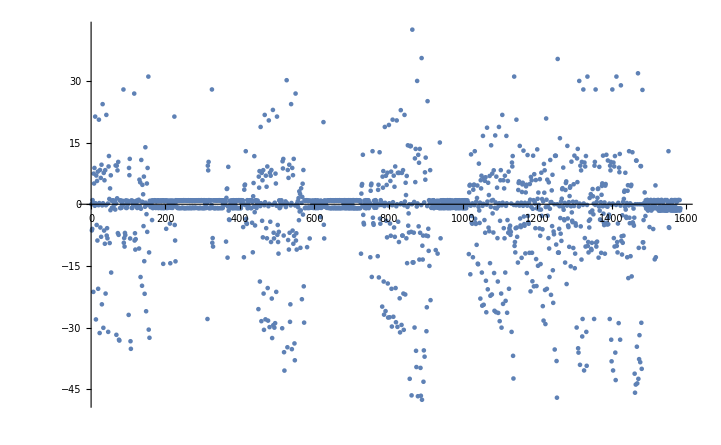

```mathematica
$fjm=DeleteDuplicates@Flatten@$jm;
$fjm//Length
ListPlot[$fjm,PlotRange->Full]
```

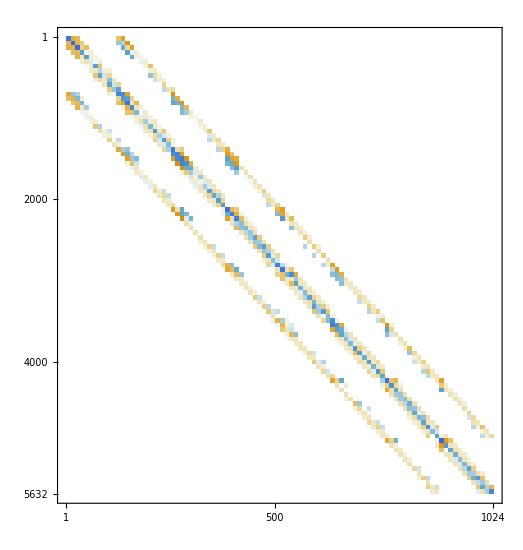

```mathematica
$jm//MatrixPlot
```

```mathematica
$sol2=LeastSquares[SetPrecision[$jm,30],SetPrecision[$b,30],Method->"Krylov"];
"maximum error versus Mathematica high precision solution"
Max[$sol2-SetPrecision[$h,30]]
```